# Math 223: Homework 1

Hardeep Bassi

02/05/2023

## Problem 1

Use the Series command to compute the Taylor series of (1+x)^(1+x) about 𝑥 = 0. Explore different
parameter values to make sure you understand how to use this command. Use the Plot command to
plot a comparison of this function with the polynomial of degree 4 given by the partial sum of the
Taylor series over the interval [-1,4]

```mathematica
Series[(1+x)^(1/x),{x,0,8}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760-(959 ⅇ x^5)/2304+(238043 ⅇ x^6)/580608-(67223 ⅇ x^7)/165888+(559440199 ⅇ x^8)/1393459200+O[x]^9

```mathematica
Series[(1+x)^(1/x),{x,0,10}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760-(959 ⅇ x^5)/2304+(238043 ⅇ x^6)/580608-(67223 ⅇ x^7)/165888+(559440199 ⅇ x^8)/1393459200-(123377159 ⅇ x^9)/309657600+(29128857391 ⅇ x^10)/73574645760+O[x]^11

```mathematica
Series[(1+x)^(1/x),{x,0,12}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760-(959 ⅇ x^5)/2304+(238043 ⅇ x^6)/580608-(67223 ⅇ x^7)/165888+(559440199 ⅇ x^8)/1393459200-(123377159 ⅇ x^9)/309657600+(29128857391 ⅇ x^10)/73574645760-(5267725147 ⅇ x^11)/13377208320+(9447595434410813 ⅇ x^12)/24103053950976000+O[x]^13

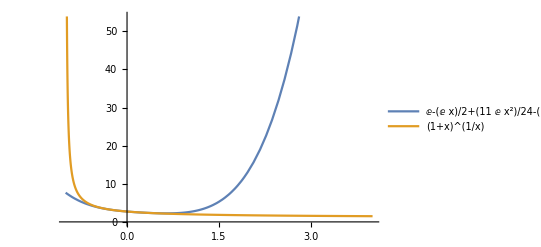

```mathematica
Plot[{Evaluate[Normal[Series[(1+x)^(1/x),{x,0,4}]]], (1+x)^(1/x)},{x,-1,4}, PlotLegends->"Expressions"]
```

## Problem 2

Use the Integrate command to compute ∫_0^(3/2) sin(x^2)dx. Then use Series within Integrate to integrate the polynomial of degree 6 given by the partial sum of the Taylor series of sin(x^2) about x =0. Use the N command to compute the absolute error made by this approximation.

```mathematica
int = Integrate[Sin[x^2], {x,0,3/2}]
```

√(π/2) FresnelS[3/(√(2 π))]

```mathematica
ps = Integrate[Series[Sin[x^2],{x,0,6}],{x,0,3/2} ]
```

1287/1792

```mathematica
Abs[N[ps - int]]
```

0.0600458

## Problem 3

Use the DSolve command to solve the following two-point boundary value problem (in the Homework 1 pdf). Read the documentation to learn how to plot the solution for different values of 0<ϵ≤1. Comment on how the solution changes with ϵ.

```mathematica
DSolve[{ϵ*y''[x] + (1+ϵ )*y'[x] + y[x] == 0, y[0]==0, y[1]==E^(-1)},y[x], {x,0,1}]
```

{{y[x]→(ⅇ^(-(-1+x+x ϵ)/ϵ) (-ⅇ^x+ⅇ^(x/ϵ)))/(-ⅇ+ⅇ^(1/ϵ))}}

```mathematica
Manipulate[Plot[(ⅇ^(-(-1+x+x ϵ)/ϵ) (-ⅇ^x+ⅇ^(x/ϵ)))/(-ⅇ+ⅇ^(1/ϵ)), {x,0,1}],{ϵ ,0.01,0.99}]
```

Using the Manipulate command, we can plot the result with differing values for ϵ, specified by the scroll bar. Using said scroll bar, we see that as ϵ→0, the solution to the BVP is unreasonable around 0 due to the solution of the BVP when ϵ = 0, being y(x)==C e^-x. Because this is the solution, we see that the given the boundary conditions of y(0)==0,y(1)==e^-1 will never hold.